# Meal Tracker Development

## Set Meal Tracker Cloud Path and Databin

This will be the directory where your meal tracker is deployed in the Wolfram Cloud.
Using a relative path, like this one, will be inside your user’s “home” cloud directory.

```mathematica
$MealTrackerCloudObject=CloudObject["MealTracker/Andrew"]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker/Andrew]

```mathematica
$MealTrackerHistoryDatabin=Databin["YourDatabinIDGoesHere"]
```

## Create or Update Default User Data

This needs to be done whenever there is a code change to the underlying EntityStores.

### Default “MyFood” EntityStore

#### Create new entity store from scratch (Old, loses data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
EntityUnregister["MyFood"]
Internal`ClearEntityValueCache["MyFood"]
AbsoluteTiming[store=GenerateEntityStore[$MealTrackerCloudObject,"MyFood",{"white bread", "peanut butter", "jelly","milk","oats","greek yogurt","flax seed","honey","vanilla extract"}];]
EntityRegister[store]
```

#### Create new EntityStore from an old EntityStore (Preferred, keeps data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
LoadEntityStore[$MealTrackerCloudObject,"MyFood"]
```

{MyFood}

```mathematica
oldStore=Entity["MyFood"]["EntityStore"];
```

```mathematica
oldEntityData=oldStore[[1,"Types","MyFood","Entities"]];
oldEntityData//Keys
```

{WhiteBread,PeanutButter,Jelly,Milk,GreekYogurt,FlaxSeed,Honey,VanillaExtract,Egg,Oats}

#### Update basic data for test deployments (OPTIONAL)

```mathematica
newBasicData=Join[
oldEntityData[[;;9]],
<|"Oats"-><|"Label"->"Oats","Food"->Entity["Food","QuakerOatsOldFashioned::8t545"],"ServingSizeString"->"0.5 cup;40. g","ServingSizes"->{Quantity[0.5, "Cups"],Quantity[40., "Grams"]},"Description"->"Oats","ServingSize"->"0.5 cup;40. g","TotalCalories"->Quantity[150., "LargeCalories"],"Calcium"->Quantity[0., "Milligrams"],"Cholesterol"->Quantity[0., "Milligrams"],"Iron"->Quantity[1.8, "Milligrams"],"Sodium"->Quantity[0., "Milligrams"],"TotalCarbohydrates"->Quantity[27., "Grams"],"TotalFat"->Quantity[3., "Grams"],"TotalFiber"->Missing["NoInput"],"TotalProtein"->Quantity[5., "Grams"],"TotalSaturatedFat"->Quantity[0.5, "Grams"],"VitaminC"->Quantity[0., "Milligrams"],"Resubmit"->True,"Entity"->Entity["Food","QuakerOatsOldFashioned::8t545"],"DateCreated"->DateObject[{2018,3,29,11,57,46.197763`8.417195923159113},"Instant","Gregorian",-5.],"DateModified"->DateObject[{2018,3,29,11,57,46.198024`8.4171983767528},"Instant","Gregorian",-5.]|>|>
];
```

```mathematica
cleanerBasicData=RotateLeft[Prepend[#,"DateCreated"->Lookup[#,"DateCreated",Lookup[#,"DateModified",Now]]]]&/@(KeyDrop[{"Description","ServingSize","Entity"}]/@newBasicData);
```

```mathematica
(* Use this to create a new data file for updating the default *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"Default","MyFood"}]]
Export[StringReplace[DateString["ISODateTime"],{"T"->"_",":"->"-"}]<>".m",
cleanerBasicData
]
```

C:\Users\andrews\Stash\open-source-meal-tracking\MealTrackerApp\Default\MyFood

2018-04-23_13-25-38.m

#### Test EntityStore

```mathematica
EntityUnregister["MyFood"]
Internal`ClearEntityValueCache["MyFood"]
AbsoluteTiming[store=GenerateEntityStore[$MealTrackerCloudObject,"MyFood",oldEntityData];]
EntityRegister[store]
```

{0.155207,Null}

{MyFood}

```mathematica
EntityValue["MyFood","EntityCount"]
```

10

#### Update EntityStore in cloud

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
UpdateEntityStore[$MealTrackerCloudObject,"MyFood",store]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker/Andrew/MyFood/2018-08-13_11-13-02.WXF]

```mathematica
LoadEntityStore[$MealTrackerCloudObject,"MyFood"]
```

{MyFood}

```mathematica
EntityValue["MyFood","EntityCount"]
```

10

### Default “MyMeal” EntityStore

#### Create new EntityStore from scratch (Old, loses data)

This loads from the latest file in MealTrackerApp/Default/MyMeal/

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
EntityUnregister["MyMeal"]
Internal`ClearEntityValueCache["MyMeal"]
AbsoluteTiming[mealStore=GenerateEntityStore[$MealTrackerCloudObject,"MyMeal"];]
EntityRegister[mealStore]
```

{0.384265,Null}

{MyMeal}

#### Create new EntityStore from an old EntityStore (Preferred, keeps data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
LoadEntityStore[$MealTrackerCloudObject,"MyMeal"]
```

{MyMeal}

```mathematica
oldStore=Entity["MyMeal"]["EntityStore"];
```

```mathematica
oldEntityData=oldStore[[1,"Types","MyMeal","Entities"]];
oldEntityData//Keys
```

{PB&JSandwich,OvernightOats}

```mathematica
EntityUnregister["MyMeal"]
Internal`ClearEntityValueCache["MyMeal"]
AbsoluteTiming[mealStore=GenerateEntityStore[$MealTrackerCloudObject,"MyMeal",oldEntityData];]
EntityRegister[mealStore]
```

{0.131561,Null}

{MyMeal}

#### Update EntityStore in cloud

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
```

```mathematica
UpdateEntityStore[$MealTrackerCloudObject,"MyMeal",mealStore]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker/Andrew/MyMeal/2018-08-13_11-14-06.WXF]

## Run test suites

### Deployment and full-system tests

This deploys a meal tracker instance to a temporary test cloud directory that is removed at the end of the test.
This test suite takes a few minutes to run.

```mathematica
CloudConnect[]
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["MealTrackerApp.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

#### Visualize timing results

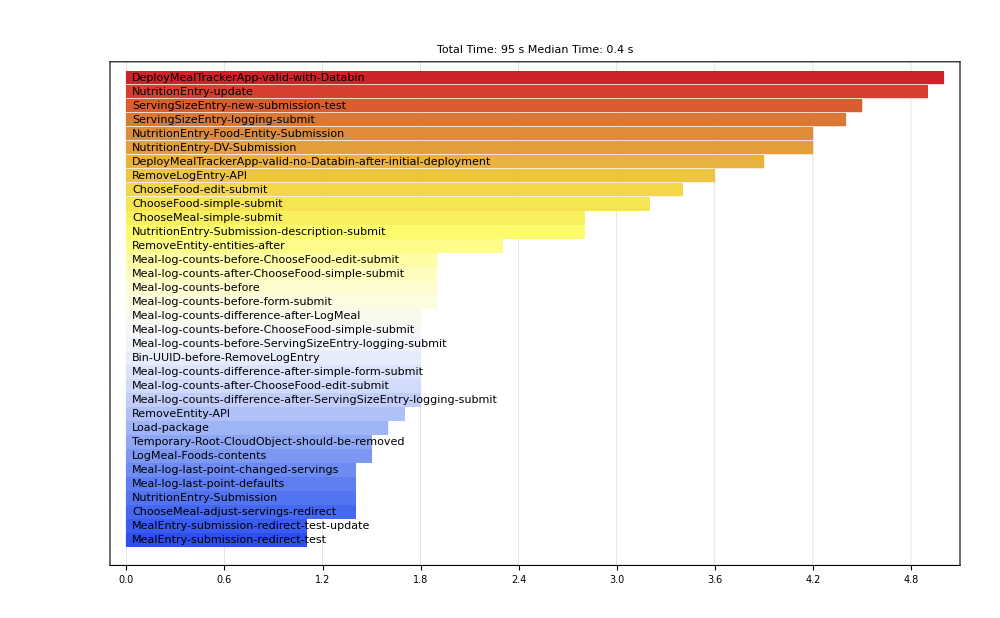

```mathematica
times=KeySelect[Association[#["TestID"]-> #["AbsoluteTimeUsed"]&/@Values[results["TestResults"]]],MatchQ[_String]];
appreciableTimes=Sort[times]//Select[#>Quantity[1,"Seconds"]&];
appreciableTimes=Round[#,0.1]&/@appreciableTimes;
BarChart[appreciableTimes,
BarOrigin->Left,
ImageSize->1000,
ChartLabels->Placed[Style[#,Black]&/@Keys[appreciableTimes],Left],
PlotTheme->"Detailed",
ChartStyle->"TemperatureMap",
PlotLabel->StringTemplate["Total Time: `` \nMedian Time: ``"][Round@Total[times],Round[Median[times],0.1]]
]
```

### General Utility tests

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["General.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{9.18881,TestReportObject[…]}

### EntityStore Utility tests

TODO: This test suite requires that the main package be loaded!

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["EntityStore.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{0.914506,TestReportObject[…]}

### GenerateData tests

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Utilities"}]];
AbsoluteTiming[results=TestReport["GenerateData.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{16.8573,TestReportObject[…]}

### RadarPlot tests

```mathematica
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["Plots/RadarPlot.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{1.66331,TestReportObject[…]}

### NutritionRadarPlot tests

```mathematica
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[results=TestReport["Plots/NutritionRadarPlot.wlt"]]
With[
{failedTestData=KeyDrop[{(*"AbsoluteTimeUsed",*)"CPUTimeUsed","MemoryUsed","TestIndex","Outcome"}]/@First/@Values[Join@@Values[results["TestsFailed"]]]},
If[Length[failedTestData]>0,
Grid[
Prepend[Values/@failedTestData,Keys[First[failedTestData]]],
Frame->All
(*,Background->{Automatic,{LightGray,None}}*)
]
]
]
```

{1.22662,TestReportObject[…]}

## Redeploy App to cloud

### Re-deploy and overwrite all data (typically not needed)

#### Create a databin

```mathematica
Databin;
DataDropClient`$JavaCompatibleQ=False;
bin=CreateDatabin["Name" -> "Meal Tracker 2/23/2018 #3"]
```

Databin[…]

#### Redeploy

```mathematica
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]

Print["Copying entity stores to disk..."];
If[Not@DirectoryQ["MyFood_History"],CreateDirectory["MyFood_History"]];
If[Not@DirectoryQ["MyMeal_History"],CreateDirectory["MyMeal_History"]];
CopyFile[#,FileNameJoin[{"MyFood_History",FileNameTake[First@#]}]]&/@CloudObjects[FileNameJoin[{$MealTrackerCloudObject,"MyFood"}]];
CopyFile[#,FileNameJoin[{"MyMeal_History",FileNameTake[First@#]}]]&/@CloudObjects[FileNameJoin[{$MealTrackerCloudObject,"MyMeal"}]];

Print["Deploying app..."];
DeployMealTrackerApp[$MealTrackerCloudObject,"DefaultDirectory"->Automatic,"HistoryDatabin"->$MealTrackerHistoryDatabin,"OverwriteExistingData"->True]
```

Copying entity stores to disk...

Deploying app...

{CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Home],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MealEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/NutritionEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewHistory],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveLogEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodSearch],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodLookup],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveEntity]}

### Copy old EntityStore WXF’s to the Cloud (typically not needed)

```mathematica
SetDirectory[NotebookDirectory[]];
CopyFile["MyFood_History\\2018-03-20_16-22-06.WXF",FileNameJoin[{$MealTrackerCloudObject,"MyFood","2018-03-20_16-22-06.WXF"}]]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyFood/2018-03-20_16-22-06.WXF]

```mathematica
SetDirectory[NotebookDirectory[]];
CopyFile["MyMeal_History\\2018-03-20_16-11-39.WXF",FileNameJoin[{$MealTrackerCloudObject,"MyMeal","2018-03-20_16-11-39.WXF"}]]
```

CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MyMeal/2018-03-20_16-11-39.WXF]

### Re-deploy without changing EntityStore data (most common operation)

```mathematica
CloudConnect[]
SetDirectory[NotebookDirectory[]];
Get["MealTrackerApp.wl"]
DeployMealTrackerApp[$MealTrackerCloudObject,"DefaultDirectory"->Automatic]
(* Handy trick to open a page immediately after deployment *)
(*%[[-1]]//SystemOpen*)
```

{CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Home],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/MealEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/NutritionEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseMeal],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ChooseFood],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ViewHistory],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveLogEntry],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodSearch],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/FoodLookup],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/RemoveEntity],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ServingSizeMultiplication],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Settings],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Reminders],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/ScanBarcode],CloudObject[https://www.wolframcloud.com/objects/andrews/MealTracker_2-23-2018/Suggestion]}

### Load EntityStores for local debugging purposes

```mathematica
LoadEntityStore[$MealTrackerCloudObject,"MyFood"]//AbsoluteTiming
LoadEntityStore[$MealTrackerCloudObject,"MyMeal"]//AbsoluteTiming
```

{0.407144,{MyFood}}

{0.254044,{MyMeal}}